### Attempt with DSolve

```mathematica
pde=D[u[x,t],t]==d D[u[x,t],{x,2}]-c D[u[x,t],x]
```

u^(0,1)[x,t]==-c u^(1,0)[x,t]+d u^(2,0)[x,t]

```mathematica
soln=DSolve[{pde,u[x,0]==0,u[0,t]==300,D[u[x,t],x]==0/.x->6},u[x,t],{x,t}]
```

DSolve[{u^(0,1)[x,t]==-c u^(1,0)[x,t]+d u^(2,0)[x,t],u[x,0]==0,u[0,t]==300,u^(1,0)[6,t]==0},u[x,t],{x,t}]

```mathematica
f[x_,t_]=u[x,t]/.soln[[1]]
```

ReplaceAll::reps: SuperscriptBox[u[x, 0] == 0u[0, t] == 300SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

u[x,t]/.{u^(0,1)[x,t]==-c u^(1,0)[x,t]+d u^(2,0)[x,t],u[x,0]==0,u[0,t]==300,u^(1,0)[6,t]==0}

### FAIL!

### Attempt using Laplace Transform

```mathematica
pde=D[u[x,t],t]==d D[u[x,t],{x,2}]-c D[u[x,t],x]
```

u^(0,1)[x,t]==-c u^(1,0)[x,t]+d u^(2,0)[x,t]

```mathematica
ibc={u[x,0]==0,u[0,t]==300,D[u[x,t],x]==0/.x->6}
```

{u[x,0]==0,u[0,t]==300,u^(1,0)[6,t]==0}

```mathematica
teqn=LaplaceTransform[pde,t,s]/.Rule@@@ibc
```

s LaplaceTransform[u[x,t],t,s]==-c LaplaceTransform[u^(1,0)[x,t],t,s]+d LaplaceTransform[u^(2,0)[x,t],t,s]

```mathematica
tsol=DSolve[teqn/.HoldPattern@LaplaceTransform[a_,t,s]:>a,u[x,t],x]
```

{{u[x,t]→ⅇ^(((c+√(c^2+4 d s)) x)/(2 d)) C[1]+ⅇ^(-((-c+√(c^2+4 d s)) x)/(2 d)) C[2]}}

```mathematica
sol=InverseLaplaceTransform[tsol[[1,1,2]],s,t]//FullSimplify
```

Undefined

### FAIL!

### Attempt using NDSolve

NDSolve attempts to provide an approximate solution with error approximately ≤10^-6.

```mathematica
da=1.0;
ca=0.1;
pde=D[u[x,t],t]==da D[u[x,t],{x,2}]-ca D[u[x,t],x];
ibc={u[x,0]==0,u[0,t]==300,D[u[x,t],x]==0/.x->6};
```

```mathematica
nsol=NDSolve[{pde,ibc[[1]],ibc[[2]],ibc[[3]]},u[x,t],{x,0,6},{t,0,2}]
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

{{u[x,t]→InterpolatingFunction[{{0., 6.}, {0., 2.}}, <>][x,t]}}

A warning is generated because the initial conditions and boundary conditions give two different values for the value of  u(0,0). Essentially, u(x,t) changes instantly at x=0. One way to avoid the inconsistent conditions on the solution is to replace the discontinuous condition with a similar condition that changes quickly but smoothly:

```mathematica
ibc2={u[x,0]==0,u[0,t]==300/(1+300Exp[-100000t])-300/301,D[u[x,t],x]==0/.x->6};
nsol2a=NDSolve[{pde,ibc2[[1]],ibc2[[2]],ibc2[[3]]},u[x,t],{x,0,6},{t,0,2}]
```

{{u[x,t]→InterpolatingFunction[{{0., 6.}, {0., 2.}}, <>][x,t]}}

```mathematica
rowHeadings=Table[x,{x,0,6,0.5}];
columnHeadings={"t=0.1","t=0.25","t=0.5","t=1.0","t=2.0"};
TableForm[Evaluate[Transpose[Table[nsol2a[[1,1,2]]/.t->a,{a,{0.1,0.25,0.5,1.0,2.0}},{x,0,6,0.5}]]],TableHeadings->{rowHeadings,columnHeadings}]
```

| t=0.1 | t=0.25 | t=0.5 | t=1.0 | t=2.0
0. | 298.947 | 298.955 | 298.966 | 298.981 | 298.995
0.5 | 79.9106 | 146.921 | 189.087 | 221.704 | 245.821
1. | 8.10945 | 49.352 | 99.6516 | 150.547 | 193.645
1.5 | 0.225456 | 10.9168 | 43.0122 | 92.9503 | 145.752
2. | -0.00452524 | 1.5393 | 15.0163 | 51.8866 | 104.57
2.5 | -0.000121682 | 0.131026 | 4.20007 | 26.0705 | 71.3697
3. | 3.04844×10^-6 | 0.00579869 | 0.93334 | 11.7489 | 46.2598
3.5 | 1.22902×10^-9 | 0.0000462 | 0.16332 | 4.73552 | 28.4389
4. | -7.78212×10^-10 | -6.02532×10^-6 | 0.0222413 | 1.70309 | 16.5738
4.5 | 1.09438×10^-11 | -1.36143×10^-7 | 0.0023124 | 0.545486 | 9.1803
5. | -3.28549×10^-14 | 4.32428×10^-9 | 0.000176995 | 0.15569 | 4.91737
5.5 | -9.21139×10^-16 | 1.56554×10^-10 | 0.000012423 | 0.0413859 | 2.76524
6. | 1.28808×10^-13 | -1.29182×10^-9 | 0.0000248419 | 0.0186388 | 2.11082

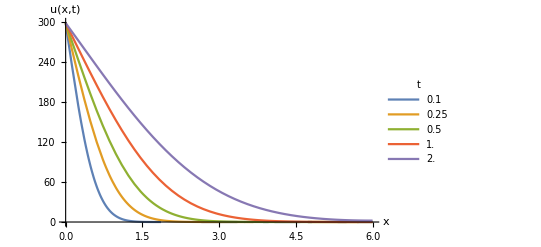

```mathematica
Plot[Evaluate[Table[nsol2a[[1,1,2]]/.t->a,{a,{0.1,0.25,0.5,1.0,2.0}}]],{x,0,6},PlotLegends->LineLegend[{0.1,0.25,0.5,1.0,2.0},LegendLabel->t],PlotRange->{0,300},AxesLabel->{x,u[x,t]}]
```

### SUCCESS (I think)!

| t=0.1 | t=0.25 | t=0.5 | t=1.0 | t=2.0
0. | 298.948 | 298.955 | 298.966 | 298.981 | 298.995
0.5 | 219.188 | 289.285 | 298.512 | 298.976 | 298.994
1. | 75.4295 | 251.755 | 295.983 | 298.96 | 298.993
1.5 | 9.73298 | 176.349 | 287.196 | 298.893 | 298.993
2. | 0.44437 | 89.7312 | 265.426 | 298.647 | 298.992
2.5 | 0.036323 | 30.9478 | 225.229 | 297.881 | 298.99
3. | 0.00159757 | 6.94081 | 168.821 | 295.83 | 298.989
3.5 | 0.0000344406 | 1.00199 | 108.059 | 291.084 | 298.986
4. | 5.865×10^-6 | 0.1007 | 57.5389 | 281.536 | 298.981
4.5 | -1.62106×10^-7 | 0.00875346 | 25.012 | 264.777 | 298.968
5. | 1.69441×10^-8 | 0.000687152 | 8.76351 | 239.065 | 298.936
5.5 | -2.882×10^-9 | 0.000040897 | 2.4603 | 205.158 | 298.869
6. | 4.58177×10^-9 | 0.0000518123 | 0.801491 | 179.161 | 298.799

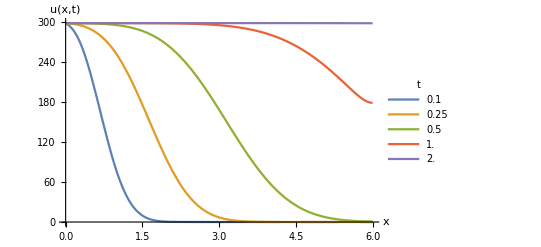

```mathematica
db=1.0;
cb=6.0;
pde=D[u[x,t],t]==db D[u[x,t],{x,2}]-cb D[u[x,t],x];
ibc2={u[x,0]==0,u[0,t]==300/(1+300Exp[-100000t])-300/301,D[u[x,t],x]==0/.x->6};
nsol2b=NDSolve[{pde,ibc2[[1]],ibc2[[2]],ibc2[[3]]},u[x,t],{x,0,6},{t,0,2}];
rowHeadings=Table[x,{x,0,6,0.5}];
columnHeadings={"t=0.1","t=0.25","t=0.5","t=1.0","t=2.0"};
TableForm[Evaluate[Transpose[Table[nsol2b[[1,1,2]]/.t->a,{a,{0.1,0.25,0.5,1.0,2.0}},{x,0,6,0.5}]]],TableHeadings->{rowHeadings,columnHeadings}]
Plot[Evaluate[Table[nsol2b[[1,1,2]]/.t->a,{a,{0.1,0.25,0.5,1.0,2.0}}]],{x,0,6},PlotLegends->LineLegend[{0.1,0.25,0.5,1.0,2.0},LegendLabel->t],PlotRange->{0,300},AxesLabel->{x,u[x,t]}]
```

| t=0.1 | t=0.25 | t=0.5 | t=1.0 | t=2.0
0. | 298.947 | 298.955 | 298.966 | 298.981 | 298.995
0.5 | 98.6791 | 179.447 | 227.695 | 261.98 | 283.311
1. | 12.3761 | 74.4162 | 146.532 | 213.397 | 261.034
1.5 | 0.495063 | 20.4271 | 77.8981 | 159.822 | 232.679
2. | 0.00310548 | 3.6095 | 33.677 | 109.107 | 199.746
2.5 | 0.000123128 | 0.399649 | 11.7122 | 67.4409 | 164.499
3. | 2.12581×10^-6 | 0.0267741 | 3.25103 | 37.5518 | 129.531
3.5 | -2.66742×10^-8 | 0.00104624 | 0.715783 | 18.7616 | 97.2628
4. | 1.4249×10^-9 | 0.0000253418 | 0.124326 | 8.38561 | 69.5147
4.5 | -2.64743×10^-11 | 5.96478×10^-7 | 0.0169482 | 3.34527 | 47.3044
5. | 3.17564×10^-13 | 1.1911×10^-8 | 0.00180465 | 1.19061 | 30.9428
5.5 | -1.04796×10^-14 | -1.83782×10^-10 | 0.000162834 | 0.388904 | 20.4723
6. | -3.57299×10^-14 | 6.78287×10^-9 | 0.000132516 | 0.186605 | 16.5502

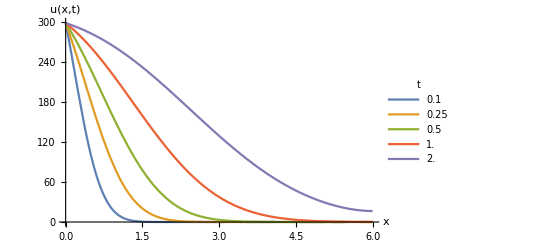

```mathematica
dc=1.0;
cc=1.0;
pde=D[u[x,t],t]==dc D[u[x,t],{x,2}]-cc D[u[x,t],x];
ibc2={u[x,0]==0,u[0,t]==300/(1+300Exp[-100000t])-300/301,D[u[x,t],x]==0/.x->6};
nsol2c=NDSolve[{pde,ibc2[[1]],ibc2[[2]],ibc2[[3]]},u[x,t],{x,0,6},{t,0,2}];
rowHeadings=Table[x,{x,0,6,0.5}];
columnHeadings={"t=0.1","t=0.25","t=0.5","t=1.0","t=2.0"};
TableForm[Evaluate[Transpose[Table[nsol2c[[1,1,2]]/.t->a,{a,{0.1,0.25,0.5,1.0,2.0}},{x,0,6,0.5}]]],TableHeadings->{rowHeadings,columnHeadings}]
Plot[Evaluate[Table[nsol2c[[1,1,2]]/.t->a,{a,{0.1,0.25,0.5,1.0,2.0}}]],{x,0,6},PlotLegends->LineLegend[{0.1,0.25,0.5,1.0,2.0},LegendLabel->t],PlotRange->{0,300},AxesLabel->{x,u[x,t]}]
```

## 1. Diffusion Dominated

#### Eqn. 1

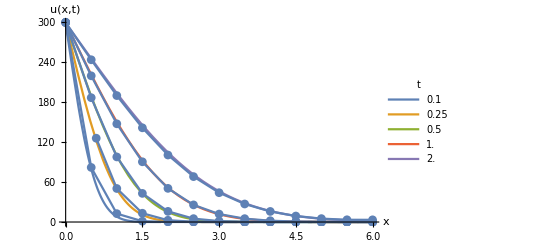

```mathematica
Δx=.5;
Δt=.01;
len1=.1/Δt;
len2=.25/Δt;
len3=.5/Δt;
len4=1/Δt;
len5=2/Δt;
yvec=List[List[300,0,0,0,0,0,0,0,0,0,0,0,0]];
AppendTo[yvec,List[]];
Do[
PrependTo[yvec[[n+1]],300];
Do[AppendTo[yvec[[n+1]],Δt(-ca(yvec[[n]][[j+1]]-yvec[[n]][[j]])/(2Δx)+da(yvec[[n]][[j+2]]-2yvec[[n]][[j+1]]+yvec[[n]][[j]])/Δx^2)+yvec[[n]][[j+1]]], {j,11}];
AppendTo[yvec[[n+1]],yvec[[n]][[12]]];
AppendTo[yvec,List[]];
,{n,len5-1}]
TableForm[yvec];
Show[Plot[Evaluate[Table[nsol2a[[1,1,2]]/.t->a,{a,{0.1,0.25,0.5,1.0,2.0}}]],{x,0,6},PlotLegends->LineLegend[{0.1,0.25,0.5,1.0,2.0},LegendLabel->t],PlotRange->{0,300},AxesLabel->{x,u[x,t]}],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len1]]}], PlotMarkers->Automatic, PlotRange->{0,300}],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len2]]}], PlotMarkers->Automatic],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len3]]}], PlotMarkers->Automatic],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len4]]}], PlotMarkers->Automatic],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len5]]}], PlotMarkers->Automatic]]
```

#### Eqn. 2

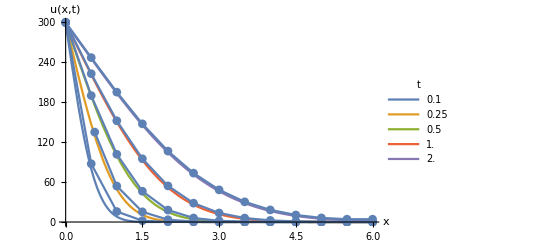

```mathematica
yvec=List[List[300,0,0,0,0,0,0,0,0,0,0,0,0]];
AppendTo[yvec,List[]];
Do[
PrependTo[yvec[[n+1]],300];
Do[AppendTo[yvec[[n+1]],Δt(-ca(yvec[[n]][[j+1]]-yvec[[n]][[j]])/Δx+da(yvec[[n]][[j+2]]-2yvec[[n]][[j+1]]+yvec[[n]][[j]])/Δx^2)+yvec[[n]][[j+1]]], {j,11}];
AppendTo[yvec[[n+1]],yvec[[n]][[12]]];
AppendTo[yvec,List[]];
,{n,len5-1}]
TableForm[yvec];
Show[Plot[Evaluate[Table[nsol2a[[1,1,2]]/.t->a,{a,{0.1,0.25,0.5,1.0,2.0}}]],{x,0,6},PlotLegends->LineLegend[{0.1,0.25,0.5,1.0,2.0},LegendLabel->t],PlotRange->{0,300},AxesLabel->{x,u[x,t]}],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len1]]}], PlotMarkers->Automatic, PlotRange->{0,300}],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len2]]}], PlotMarkers->Automatic],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len3]]}], PlotMarkers->Automatic],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len4]]}], PlotMarkers->Automatic],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len5]]}], PlotMarkers->Automatic]]
```

#### Eqn. 3

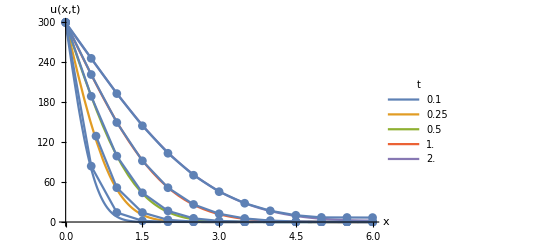

```mathematica
yvec=List[List[300,0,0,0,0,0,0,0,0,0,0,0,0]];
AppendTo[yvec,List[]];
Do[
PrependTo[yvec[[n+1]],300];
AppendTo[yvec[[n+1]],Δt(-ca(yvec[[n]][[2]]-yvec[[n]][[1]])/Δx+da(yvec[[n]][[3]]-2yvec[[n]][[2]]+yvec[[n]][[1]])/Δx^2)+yvec[[n]][[2]]]
Do[AppendTo[yvec[[n+1]],Δt(-ca(yvec[[n]][[j+3]]-yvec[[n]][[j+2]])/Δx+da 1/Δx^2((Δt(-ca(yvec[[n]][[j+4]]-yvec[[n]][[j+3]])/Δx+da(yvec[[n]][[j+4]]-2yvec[[n]][[j+3]]+yvec[[n]][[j+2]])/Δx^2)+yvec[[n]][[j+3]])-2(Δt(-ca(yvec[[n]][[j+3]]-yvec[[n]][[j+2]])/Δx+da(yvec[[n]][[j+3]]-2yvec[[n]][[j+2]]+yvec[[n]][[j+1]])/Δx^2)+yvec[[n]][[j+2]])+(Δt(-ca(yvec[[n]][[j+2]]-yvec[[n]][[j+1]])/Δx+da(yvec[[n]][[j+2]]-2yvec[[n]][[j+1]]+yvec[[n]][[j]])/Δx^2)+yvec[[n]][[j+1]])))+yvec[[n]][[j+2]]], {j,9}];
AppendTo[yvec[[n+1]],yvec[[n]][[11]]];
AppendTo[yvec[[n+1]],yvec[[n]][[12]]];
AppendTo[yvec,List[]];
,{n,len5-1}]
TableForm[yvec];
Show[Plot[Evaluate[Table[nsol2a[[1,1,2]]/.t->a,{a,{0.1,0.25,0.5,1.0,2.0}}]],{x,0,6},PlotLegends->LineLegend[{0.1,0.25,0.5,1.0,2.0},LegendLabel->t],PlotRange->{0,300},AxesLabel->{x,u[x,t]}],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len1]]}], PlotMarkers->Automatic, PlotRange->{0,300}],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len2]]}], PlotMarkers->Automatic],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len3]]}], PlotMarkers->Automatic],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len4]]}], PlotMarkers->Automatic],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len5]]}], PlotMarkers->Automatic]]
```

## II. Convection Dominated

#### Eqn. 1

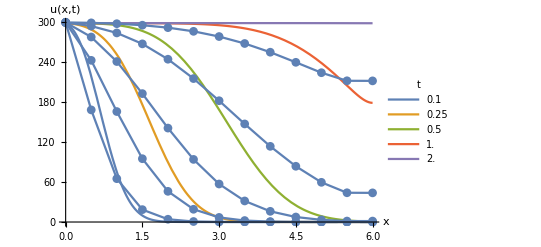

```mathematica
yvec=List[List[300,0,0,0,0,0,0,0,0,0,0,0,0]];
AppendTo[yvec,List[]];
Do[
PrependTo[yvec[[n+1]],300];
Do[AppendTo[yvec[[n+1]],Δt(-cb(yvec[[n]][[j+1]]-yvec[[n]][[j]])/(2Δx)+db(yvec[[n]][[j+2]]-2yvec[[n]][[j+1]]+yvec[[n]][[j]])/Δx^2)+yvec[[n]][[j+1]]], {j,11}];
AppendTo[yvec[[n+1]],yvec[[n]][[12]]];
AppendTo[yvec,List[]];
,{n,len5-1}]
TableForm[yvec];
Show[Plot[Evaluate[Table[nsol2b[[1,1,2]]/.t->a,{a,{0.1,0.25,0.5,1.0,2.0}}]],{x,0,6},PlotLegends->LineLegend[{0.1,0.25,0.5,1.0,2.0},LegendLabel->t],PlotRange->{0,300},AxesLabel->{x,u[x,t]}],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len1]]}], PlotMarkers->Automatic, PlotRange->{0,300}],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len2]]}], PlotMarkers->Automatic],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len3]]}], PlotMarkers->Automatic],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len4]]}], PlotMarkers->Automatic],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len5]]}], PlotMarkers->Automatic]]
```

#### Eqn 2.

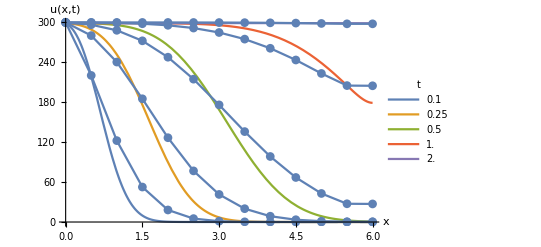

```mathematica
yvec=List[List[300,0,0,0,0,0,0,0,0,0,0,0,0]];
AppendTo[yvec,List[]];
Do[
PrependTo[yvec[[n+1]],300];
Do[AppendTo[yvec[[n+1]],Δt(-cb(yvec[[n]][[j+1]]-yvec[[n]][[j]])/Δx+db(yvec[[n]][[j+2]]-2yvec[[n]][[j+1]]+yvec[[n]][[j]])/Δx^2)+yvec[[n]][[j+1]]], {j,11}];
AppendTo[yvec[[n+1]],yvec[[n]][[12]]];
AppendTo[yvec,List[]];
,{n,len5-1}]
TableForm[yvec];
Show[Plot[Evaluate[Table[nsol2b[[1,1,2]]/.t->a,{a,{0.1,0.25,0.5,1.0,2.0}}]],{x,0,6},PlotLegends->LineLegend[{0.1,0.25,0.5,1.0,2.0},LegendLabel->t],PlotRange->{0,300},AxesLabel->{x,u[x,t]}],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len1]]}], PlotMarkers->Automatic, PlotRange->{0,300}],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len2]]}], PlotMarkers->Automatic],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len3]]}], PlotMarkers->Automatic],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len4]]}], PlotMarkers->Automatic],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len5]]}], PlotMarkers->Automatic]]
```

#### Eqn 3.

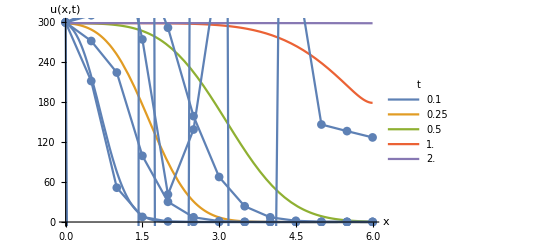

```mathematica
yvec=List[List[300,0,0,0,0,0,0,0,0,0,0,0,0]];
AppendTo[yvec,List[]];
Do[
PrependTo[yvec[[n+1]],300];
AppendTo[yvec[[n+1]],Δt(-cb(yvec[[n]][[2]]-yvec[[n]][[1]])/Δx+db(yvec[[n]][[3]]-2yvec[[n]][[2]]+yvec[[n]][[1]])/Δx^2)+yvec[[n]][[2]]]
Do[AppendTo[yvec[[n+1]],Δt(-cb(yvec[[n]][[j+3]]-yvec[[n]][[j+2]])/Δx+db 1/Δx^2((Δt(-cb(yvec[[n]][[j+4]]-yvec[[n]][[j+3]])/Δx+db(yvec[[n]][[j+4]]-2yvec[[n]][[j+3]]+yvec[[n]][[j+2]])/Δx^2)+yvec[[n]][[j+3]])-2(Δt(-cb(yvec[[n]][[j+3]]-yvec[[n]][[j+2]])/Δx+db(yvec[[n]][[j+3]]-2yvec[[n]][[j+2]]+yvec[[n]][[j+1]])/Δx^2)+yvec[[n]][[j+2]])+(Δt(-cb(yvec[[n]][[j+2]]-yvec[[n]][[j+1]])/Δx+db(yvec[[n]][[j+2]]-2yvec[[n]][[j+1]]+yvec[[n]][[j]])/Δx^2)+yvec[[n]][[j+1]])))+yvec[[n]][[j+2]]], {j,9}];
AppendTo[yvec[[n+1]],yvec[[n]][[11]]];
AppendTo[yvec[[n+1]],yvec[[n]][[12]]];
AppendTo[yvec,List[]];
,{n,len5-1}]
TableForm[yvec];
Show[Plot[Evaluate[Table[nsol2b[[1,1,2]]/.t->a,{a,{0.1,0.25,0.5,1.0,2.0}}]],{x,0,6},PlotLegends->LineLegend[{0.1,0.25,0.5,1.0,2.0},LegendLabel->t],PlotRange->{0,300},AxesLabel->{x,u[x,t]}],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len1]]}], PlotMarkers->Automatic, PlotRange->{0,300}],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len2]]}], PlotMarkers->Automatic],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len3]]}], PlotMarkers->Automatic],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len4]]}], PlotMarkers->Automatic],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len5]]}], PlotMarkers->Automatic]]
```

## III. Equal

#### Eqn. 1

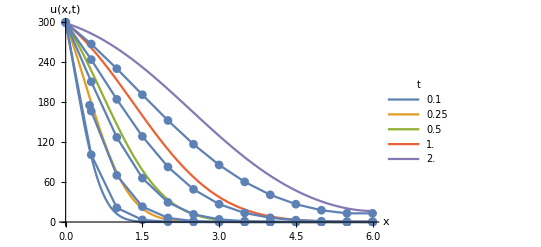

```mathematica
yvec=List[List[300,0,0,0,0,0,0,0,0,0,0,0,0]];
AppendTo[yvec,List[]];
Do[
PrependTo[yvec[[n+1]],300];
Do[AppendTo[yvec[[n+1]],Δt(-cc(yvec[[n]][[j+1]]-yvec[[n]][[j]])/(2Δx)+dc(yvec[[n]][[j+2]]-2yvec[[n]][[j+1]]+yvec[[n]][[j]])/Δx^2)+yvec[[n]][[j+1]]], {j,11}];
AppendTo[yvec[[n+1]],yvec[[n]][[12]]];
AppendTo[yvec,List[]];
,{n,len5-1}]
TableForm[yvec];
Show[Plot[Evaluate[Table[nsol2c[[1,1,2]]/.t->a,{a,{0.1,0.25,0.5,1.0,2.0}}]],{x,0,6},PlotLegends->LineLegend[{0.1,0.25,0.5,1.0,2.0},LegendLabel->t],PlotRange->{0,300},AxesLabel->{x,u[x,t]}],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len1]]}], PlotMarkers->Automatic, PlotRange->{0,300}],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len2]]}], PlotMarkers->Automatic],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len3]]}], PlotMarkers->Automatic],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len4]]}], PlotMarkers->Automatic],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len5]]}], PlotMarkers->Automatic]]
```

#### Eqn. 2

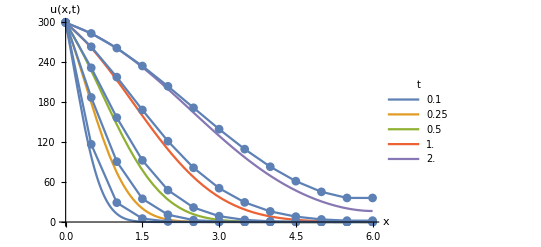

```mathematica
yvec=List[List[300,0,0,0,0,0,0,0,0,0,0,0,0]];
AppendTo[yvec,List[]];
Do[
PrependTo[yvec[[n+1]],300];
Do[AppendTo[yvec[[n+1]],Δt(-cc(yvec[[n]][[j+1]]-yvec[[n]][[j]])/Δx+dc(yvec[[n]][[j+2]]-2yvec[[n]][[j+1]]+yvec[[n]][[j]])/Δx^2)+yvec[[n]][[j+1]]], {j,11}];
AppendTo[yvec[[n+1]],yvec[[n]][[12]]];
AppendTo[yvec,List[]];
,{n,len5-1}]
TableForm[yvec];
Show[Plot[Evaluate[Table[nsol2c[[1,1,2]]/.t->a,{a,{0.1,0.25,0.5,1.0,2.0}}]],{x,0,6},PlotLegends->LineLegend[{0.1,0.25,0.5,1.0,2.0},LegendLabel->t],PlotRange->{0,300},AxesLabel->{x,u[x,t]}],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len1]]}], PlotMarkers->Automatic, PlotRange->{0,300}],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len2]]}], PlotMarkers->Automatic],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len3]]}], PlotMarkers->Automatic],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len4]]}], PlotMarkers->Automatic],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len5]]}], PlotMarkers->Automatic]]
```

#### Eqn. 3

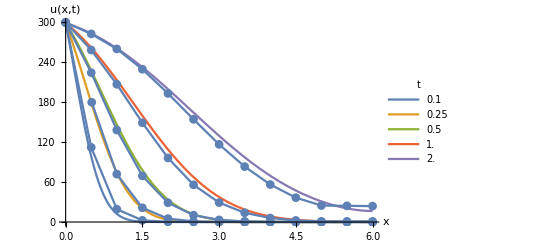

```mathematica
yvec=List[List[300,0,0,0,0,0,0,0,0,0,0,0,0]];
AppendTo[yvec,List[]];
Do[
PrependTo[yvec[[n+1]],300];
AppendTo[yvec[[n+1]],Δt(-cc(yvec[[n]][[2]]-yvec[[n]][[1]])/Δx+dc(yvec[[n]][[3]]-2yvec[[n]][[2]]+yvec[[n]][[1]])/Δx^2)+yvec[[n]][[2]]]
Do[AppendTo[yvec[[n+1]],Δt(-cc(yvec[[n]][[j+3]]-yvec[[n]][[j+2]])/Δx+dc 1/Δx^2((Δt(-cc(yvec[[n]][[j+4]]-yvec[[n]][[j+3]])/Δx+dc(yvec[[n]][[j+4]]-2yvec[[n]][[j+3]]+yvec[[n]][[j+2]])/Δx^2)+yvec[[n]][[j+3]])-2(Δt(-cc(yvec[[n]][[j+3]]-yvec[[n]][[j+2]])/Δx+dc(yvec[[n]][[j+3]]-2yvec[[n]][[j+2]]+yvec[[n]][[j+1]])/Δx^2)+yvec[[n]][[j+2]])+(Δt(-cc(yvec[[n]][[j+2]]-yvec[[n]][[j+1]])/Δx+dc(yvec[[n]][[j+2]]-2yvec[[n]][[j+1]]+yvec[[n]][[j]])/Δx^2)+yvec[[n]][[j+1]])))+yvec[[n]][[j+2]]], {j,9}];
AppendTo[yvec[[n+1]],yvec[[n]][[11]]];
AppendTo[yvec[[n+1]],yvec[[n]][[12]]];
AppendTo[yvec,List[]];
,{n,len5-1}]
TableForm[yvec];
Show[Plot[Evaluate[Table[nsol2c[[1,1,2]]/.t->a,{a,{0.1,0.25,0.5,1.0,2.0}}]],{x,0,6},PlotLegends->LineLegend[{0.1,0.25,0.5,1.0,2.0},LegendLabel->t],PlotRange->{0,300},AxesLabel->{x,u[x,t]}],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len1]]}], PlotMarkers->Automatic, PlotRange->{0,300}],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len2]]}], PlotMarkers->Automatic],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len3]]}], PlotMarkers->Automatic],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len4]]}], PlotMarkers->Automatic],
ListLinePlot[Transpose[{{0,.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},yvec[[len5]]}], PlotMarkers->Automatic]]
```